```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=0.2;
R=L/Sqrt[2];
c={L/2,h+L/2};
```

```mathematica
u0[x_,y_]:=x^3-y
```

```mathematica
(*read u_0*)
t0=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/membrane/solution/u_0_test.csv"]
t0=Table[{t0[[i,3]],t0[[i,4]],t0[[i,2]]},{i,2,Length[t0]}]
```

```mathematica
plotu0=ListPointPlot3D[t0,PlotStyle->{Green,PointSize->0.01}]
```

-Graphics3D-

```mathematica
(*read u_1*)
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/membrane/solution/u_1_test.csv"]
t1=Table[{t1[[i,3]],t1[[i,2]]},{i,2,Length[t1]}]
```

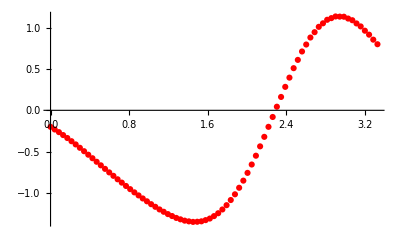

```mathematica
plotu1=ListPlot[t1,PlotStyle->Red]
```

```mathematica
Solve[{3π/2 a + b ==π+π/4,-3 π/2(1-a)+b==-π/4},{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→(5 π)/4-(3 a π)/2}}

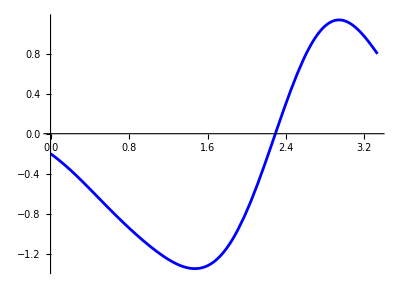

```mathematica
plotu0on1=ParametricPlot[{3π/2 R t,u0[c[[1]]+R Cos[-3π/2 t+5π/4],c[[2]]+R Sin[-3π/2 t+5π/4]]},{t,0,1},PlotStyle->Blue,AspectRatio->Full]
```

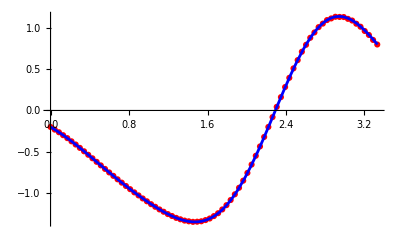

```mathematica
Show[plotu1,plotu0on1,PlotRange->Full]
```